# Cases per Lawyer Data Collapse

We plot the approximated supply of each specialty as a function of a proxy of their number of cases across MSAs.

## Import Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\ol2234\Downloads\Lawyers\Figures\Data Collapse

## Bankruptcy

```mathematica
Import["Bankruptcy_Proxy_Normalized.csv"][[1]]
```

{AREA,Bankruptcy filings,Bankruptcy}

```mathematica
BankruptcyRaw=Import["Bankruptcy_Proxy_Normalized.csv"][[2;;]];
```

```mathematica
Bankruptcy=BankruptcyRaw[[All,-2;;]];
```

```mathematica
BankruptcyMeanProxy=N[Mean[Bankruptcy[[All,1]]]];
```

```mathematica
BankruptcyMeanLawyers=N[Mean[Bankruptcy[[All,2]]]];
```

```mathematica
BankruptcyCollapse=Select[Bankruptcy,#[[1]]>0&&#[[2]]>0&]/. {a_,b_}:>{a/BankruptcyMeanProxy,b/BankruptcyMeanLawyers};
```

## Crime

```mathematica
Import["Crime_Proxy_Normalized.csv"][[1]]
```

{AREA,Criminal_Defense,Number_of_incidents,Number_of_arrests}

```mathematica
CrimeRaw=Import["Crime_Proxy_Normalized.csv"][[2;;]];
```

```mathematica
Crime=CrimeRaw[[All,{4,2}]];
```

```mathematica
CrimeMeanProxy=N[Mean[Crime[[All,1]]]];
```

```mathematica
CrimeMeanLawyers=N[Mean[Crime[[All,2]]]];
```

```mathematica
CrimeCollapse=Select[Crime,#[[1]]>0&&#[[2]]>0&]/. {a_,b_}:>{a/CrimeMeanProxy,b/CrimeMeanLawyers};
```

## Family

```mathematica
Import["Family_Proxy_Normalized.csv"][[1]]
```

{AREA,Female_Divorces,Family}

```mathematica
FamilyRaw=Import["Family_Proxy_Normalized.csv"][[2;;]];
```

```mathematica
Family=FamilyRaw[[All,-2;;]];
```

```mathematica
FamilyMeanProxy=N[Mean[Family[[All,1]]]];
```

```mathematica
FamilyMeanLawyers=N[Mean[Family[[All,2]]]];
```

```mathematica
FamilyCollapse=Select[Family,#[[1]]>0&&#[[2]]>0&]/. {a_,b_}:>{a/FamilyMeanProxy,b/FamilyMeanLawyers};
```

## Immigration

```mathematica
Import["Immigration_Proxy_Normalized.csv"][[1]]
```

{AREA,Foreign_Born_Population,Immigration}

```mathematica
ImmigrationRaw=Import["Immigration_Proxy_Normalized.csv"][[2;;]];
```

```mathematica
Immigration=ImmigrationRaw[[All,-2;;]];
```

```mathematica
ImmigrationMeanProxy=N[Mean[Immigration[[All,1]]]];
```

```mathematica
ImmigrationMeanLawyers=N[Mean[Immigration[[All,2]]]];
```

```mathematica
ImmigrationCollapse=Select[Immigration,#[[1]]>0&&#[[2]]>0&]/. {a_,b_}:>{a/ImmigrationMeanProxy,b/ImmigrationMeanLawyers};
```

## Intellectual Property

```mathematica
Import["Intellectual_Property_Proxy_Normalized.csv"][[1]]
```

{AREA,Patents,Intellectual Property}

```mathematica
IntellectualRaw=Import["Intellectual_Property_Proxy_Normalized.csv"][[2;;]];
```

```mathematica
Intellectual=IntellectualRaw[[All,-2;;]];
```

```mathematica
IntellectualMeanProxy=N[Mean[Intellectual[[All,1]]]];
```

```mathematica
IntellectualMeanLawyers=N[Mean[Intellectual[[All,2]]]];
```

```mathematica
IntellectualCollapse=Select[Intellectual,#[[1]]>0&&#[[2]]>0&]/. {a_,b_}:>{a/IntellectualMeanProxy,b/IntellectualMeanLawyers};
```

## Real Estate

```mathematica
Import["Real_Estate_Proxy_Normalized.csv"][[1]]
```

{AREA,Real Estate,Total_Transaction_Value_2024,Total_Transaction_Value_2024_millions}

```mathematica
RealEstateRaw=Import["Real_Estate_Proxy_Normalized.csv"][[2;;]];
```

```mathematica
RealEstate=RealEstateRaw[[All,{4,2}]];
```

```mathematica
RealEstateMeanProxy=N[Mean[RealEstate[[All,1]]]];
```

```mathematica
RealEstateMeanLawyers=N[Mean[RealEstate[[All,2]]]];
```

```mathematica
RealEstateCollapse=Select[RealEstate,#[[1]]>0&&#[[2]]>0&]/. {a_,b_}:>{a/RealEstateMeanProxy,b/RealEstateMeanLawyers};
```

## Scaling (OLS sanity check)

## Bankruptcy

```mathematica
logBankruptcyCollapse=Log10/@BankruptcyCollapse;
```

```mathematica
lmBankruptcy=LinearModelFit[logBankruptcyCollapse,x,x];
```

```mathematica
slopeBankruptcy=lmBankruptcy["BestFitParameters"][[2]]
slopeCIBankruptcy=lmBankruptcy["ParameterConfidenceIntervals"][[2]]
r2Bankruptcy=lmBankruptcy["RSquared"]
pValue=lmBankruptcy["ParameterPValues"][[2]]
```

1.01737

{0.959357,1.07539}

0.757781

4.68899×10^-119

## Crime

```mathematica
logCrimeCollapse=Log10/@CrimeCollapse;
```

```mathematica
lmCrime=LinearModelFit[logCrimeCollapse,x,x];
```

```mathematica
slopeCrime=lmCrime["BestFitParameters"][[2]]
slopeCICrime=lmCrime["ParameterConfidenceIntervals"][[2]]
r2Crime=lmCrime["RSquared"]
pValue=lmCrime["ParameterPValues"][[2]]
```

0.924193

{0.85657,0.991816}

0.656406

1.03845×10^-89

## Family

```mathematica
logFamilyCollapse=Log10/@FamilyCollapse;
```

```mathematica
lmFamily=LinearModelFit[logFamilyCollapse,x,x];
```

```mathematica
slopeFamily=lmFamily["BestFitParameters"][[2]]
slopeCIFamily=lmFamily["ParameterConfidenceIntervals"][[2]]
r2Family=lmFamily["RSquared"]
pValue=lmFamily["ParameterPValues"][[2]]
```

0.964249

{0.907637,1.02086}

0.756566

8.41229×10^-113

## Immigration

```mathematica
logImmigrationCollapse=Log10/@ImmigrationCollapse;
```

```mathematica
lmImmigration=LinearModelFit[logImmigrationCollapse,x,x];
```

```mathematica
slopeImmigration=lmImmigration["BestFitParameters"][[2]]
slopeCIImmigration=lmImmigration["ParameterConfidenceIntervals"][[2]]
r2Immigration=lmImmigration["RSquared"]
pValue=lmImmigration["ParameterPValues"][[2]]
```

1.05847

{0.997581,1.11936}

0.763497

2.2131×10^-115

## Intellectual Property

```mathematica
logIntellectualCollapse=Log10/@IntellectualCollapse;
```

```mathematica
lmIntellectual=LinearModelFit[logIntellectualCollapse,x,x];
```

```mathematica
slopeIntellectual=lmIntellectual["BestFitParameters"][[2]]
slopeCIIntellectual=lmIntellectual["ParameterConfidenceIntervals"][[2]]
r2Intellectual=lmIntellectual["RSquared"]
pValue=lmIntellectual["ParameterPValues"][[2]]
```

0.987916

{0.934297,1.04154}

0.799228

4.33238×10^-117

## Real Estate

```mathematica
logRealEstateCollapse=Log10/@RealEstateCollapse;
```

```mathematica
lmRealEstate=LinearModelFit[logRealEstateCollapse,x,x];
```

```mathematica
slopeRealEstate=lmRealEstate["BestFitParameters"][[2]]
slopeCIRealEstate=lmRealEstate["ParameterConfidenceIntervals"][[2]]
r2RealEstate=lmRealEstate["RSquared"]
pValue=lmRealEstate["ParameterPValues"][[2]]
```

1.04309

{0.982945,1.10323}

0.80856

4.43917×10^-101

## Plotting

## Parameters

```mathematica
TextSize=20;
```

```mathematica
TicksSize=15;
```

```mathematica
MarkerThickness=1/70;
```

```mathematica
LinesThickness=0.007;
```

```mathematica
PlotSize=500;
```

```mathematica
ColorsDiscrete=ResourceFunction["HexToColor"]/@{"#1065AB","#3893C3","#8EC4DE","#F6A482","#D75F4C","#B31529"}
```

{RGBColor[0.06274509803921569, 0.396078431372549, 0.6705882352941176],RGBColor[0.2196078431372549, 0.5764705882352941, 0.7647058823529411],RGBColor[0.5568627450980392, 0.7686274509803921, 0.8705882352941177],RGBColor[0.9647058823529412, 0.6431372549019607, 0.5098039215686274],RGBColor[0.8431372549019608, 0.37254901960784315, 0.2980392156862745],RGBColor[0.7019607843137254, 0.08235294117647059, 0.16078431372549018]}

```mathematica
ColorGradient=Blend[ColorsDiscrete,#]&
```

Blend[ColorsDiscrete,#1]&

```mathematica
colors=ColorGradient/@Rescale[Range[6]]
```

{RGBColor[0.06274509803921569, 0.396078431372549, 0.6705882352941176],RGBColor[0.2196078431372549, 0.5764705882352941, 0.7647058823529411],RGBColor[0.5568627450980392, 0.7686274509803921, 0.8705882352941177],RGBColor[0.9647058823529412, 0.6431372549019607, 0.5098039215686274],RGBColor[0.8431372549019608, 0.37254901960784315, 0.2980392156862745],RGBColor[0.7019607843137254, 0.08235294117647059, 0.16078431372549018]}

```mathematica
opacity=1;
```

## Range

```mathematica
MinX=Min[BankruptcyCollapse[[All,1]],CrimeCollapse[[All,1]],FamilyCollapse[[All,1]],ImmigrationCollapse[[All,1]],IntellectualCollapse[[All,1]],RealEstateCollapse[[All,1]]]
```

0.00276172

```mathematica
MaxX=Max[BankruptcyCollapse[[All,1]],CrimeCollapse[[All,1]],FamilyCollapse[[All,1]],ImmigrationCollapse[[All,1]],IntellectualCollapse[[All,1]],RealEstateCollapse[[All,1]]]
```

49.2158

```mathematica
MinY=Min[BankruptcyCollapse[[All,2]],CrimeCollapse[[All,2]],FamilyCollapse[[All,2]],ImmigrationCollapse[[All,2]],IntellectualCollapse[[All,2]],RealEstateCollapse[[All,2]]]
```

0.00185568

```mathematica
MaxY=Max[BankruptcyCollapse[[All,2]],CrimeCollapse[[All,2]],FamilyCollapse[[All,2]],ImmigrationCollapse[[All,2]],IntellectualCollapse[[All,2]],RealEstateCollapse[[All,2]]]
```

46.8787

```mathematica
PlotRangeCollapse={Min[10^Floor[Log10[MinX]],10^Floor[Log10[MinY]]],Max[10^Ceiling[Log10[MaxX]],10^Ceiling[Log10[MaxY]]]}
```

{1/1000,100}

## Diagonal Line

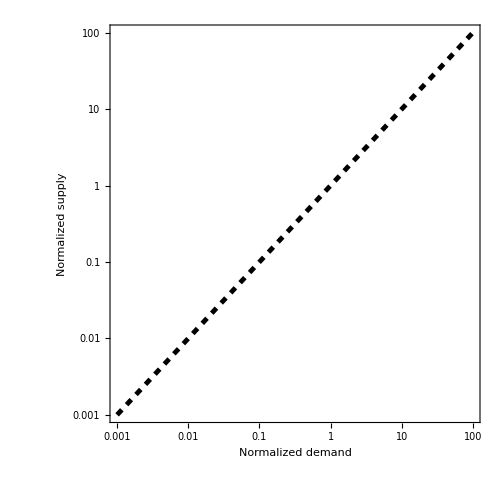

```mathematica
DiagonalPlot=LogLogPlot[x,{x,PlotRangeCollapse[[1]],PlotRangeCollapse[[2]]},PlotRange->{PlotRangeCollapse,PlotRangeCollapse},PlotStyle->{Black,Dashed,Thickness[LinesThickness]},PlotTheme->"Scientific",FrameTicksStyle->Directive[Black,TextSize,FontFamily->"Arial"],FrameTicks->{{Table[{10^i,Style[Superscript[10,i],TextSize,FontFamily->"Arial"]},{i,-3,2}],None},{Table[{10^i,Style[Superscript[10,i],TextSize,FontFamily->"Arial"]},{i,-3,2}],None}},FrameLabel->{Style["Normalized demand",TextSize,FontFamily->"Arial"],Style["Normalized supply",TextSize,FontFamily->"Arial"]},FrameStyle->Directive[Thickness[.005]],LabelStyle->Directive[Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->PlotSize,BaseStyle->{FontFamily->"Arial",FontSize->TextSize}]
```

## Bankruptcy

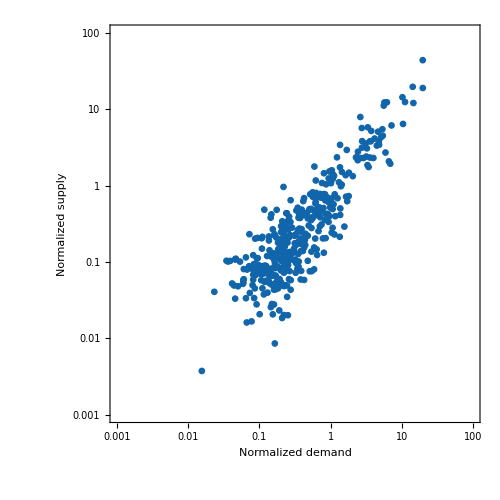

```mathematica
BankruptcyPlot=ListLogLogPlot[BankruptcyCollapse,PlotRange->{PlotRangeCollapse,PlotRangeCollapse},PlotMarkers->{Graphics[{FaceForm[colors[[1]]],EdgeForm[{colors[[1]],Opacity[opacity]}], Disk[]}],MarkerThickness},PlotTheme->"Scientific",FrameTicksStyle->Directive["Label",TextSize],FrameTicks->{{Table[{10^i,Style[Superscript[10,i],TextSize,FontFamily->"Arial"]},{i,-3,2}],None},{Table[{10^i,Style[Superscript[10,i],TextSize,FontFamily->"Arial"]},{i,-3,2}],None}},FrameLabel->{Style["Normalized demand",TextSize,FontFamily->"Arial"],Style["Normalized supply",TextSize,FontFamily->"Arial"]},PlotTheme-> "Scientific", 
FrameStyle->Directive[Thickness[.005]],LabelStyle->Directive[Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->PlotSize,BaseStyle->{FontFamily->"Arial",FontSize->TextSize}]
```

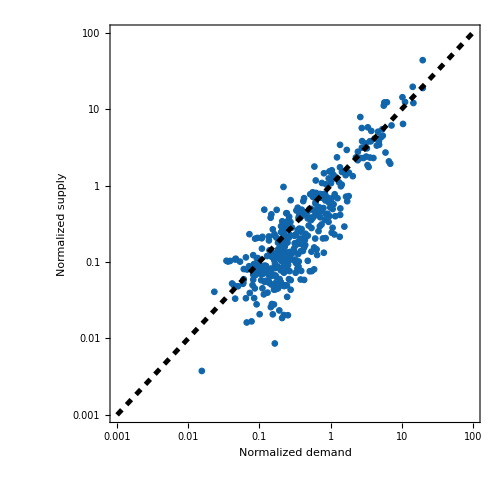

```mathematica
Show[BankruptcyPlot,DiagonalPlot]
```

## Crime

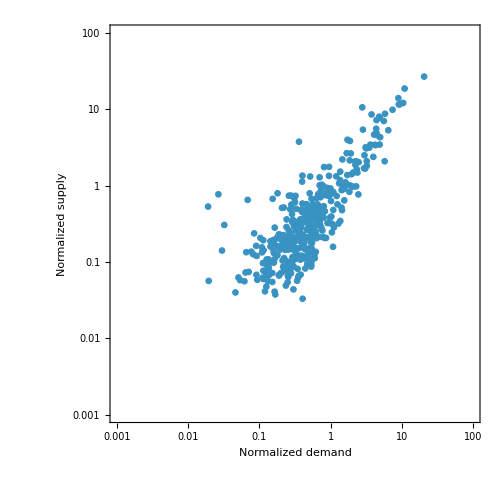

```mathematica
CrimePlot=ListLogLogPlot[CrimeCollapse,PlotRange->{PlotRangeCollapse,PlotRangeCollapse},PlotMarkers->{Graphics[{FaceForm[colors[[2]]],EdgeForm[{colors[[2]],Opacity[opacity]}], Disk[]}],MarkerThickness},PlotTheme->"Scientific",FrameTicksStyle->Directive["Label",TextSize],FrameTicks->{{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"}},None},{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"}},None}},FrameLabel->{Style["Normalized demand",TextSize],Style["Normalized supply",TextSize]},PlotTheme-> "Scientific", 
FrameStyle->Directive[Thickness[.005]],LabelStyle->Directive[Black,FontFamily->{"Arial"}],AspectRatio->1,ImageSize->PlotSize]
```

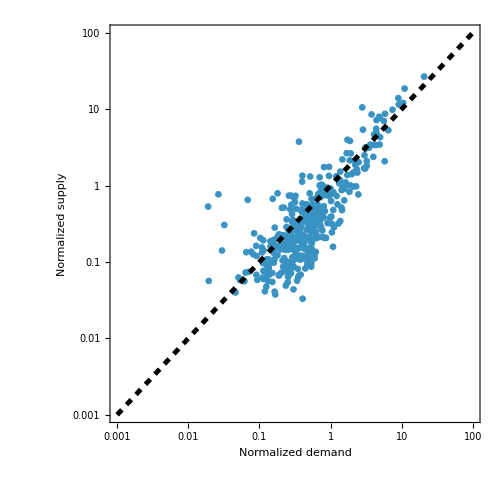

```mathematica
Show[CrimePlot,DiagonalPlot]
```

## Family

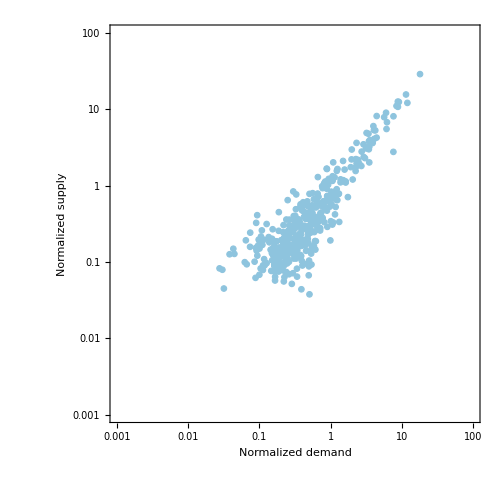

```mathematica
FamilyPlot=ListLogLogPlot[FamilyCollapse,PlotRange->{PlotRangeCollapse,PlotRangeCollapse},PlotMarkers->{Graphics[{FaceForm[colors[[3]]],EdgeForm[{colors[[3]],Opacity[opacity]}], Disk[]}],MarkerThickness},PlotTheme->"Scientific",FrameTicksStyle->Directive["Label",TextSize],FrameTicks->{{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"}},None},{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"}},None}},FrameLabel->{Style["Normalized demand",TextSize],Style["Normalized supply",TextSize]},PlotTheme-> "Scientific", 
FrameStyle->Directive[Thickness[.005]],LabelStyle->Directive[Black,FontFamily->{"Arial"}],AspectRatio->1,ImageSize->PlotSize]
```

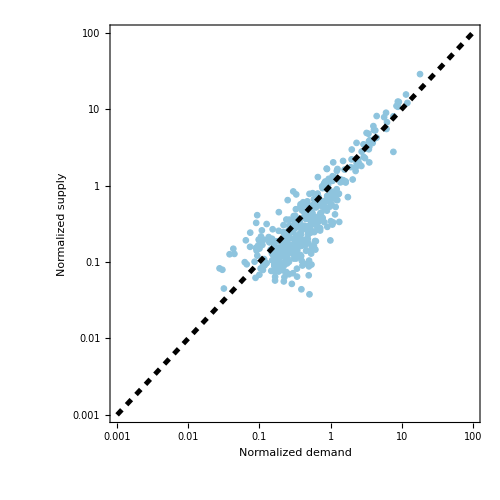

```mathematica
Show[FamilyPlot,DiagonalPlot]
```

## Immigration

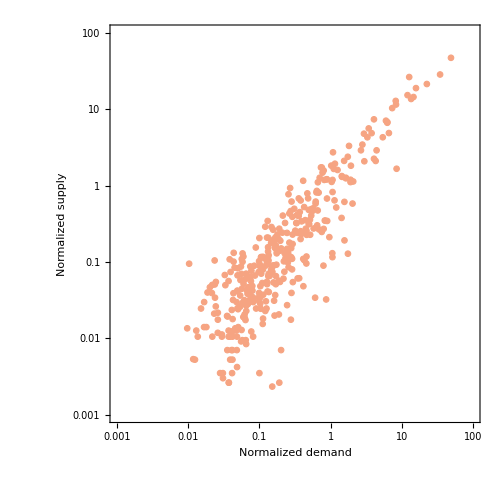

```mathematica
ImmigrationPlot=ListLogLogPlot[ImmigrationCollapse,PlotRange->{PlotRangeCollapse,PlotRangeCollapse},PlotMarkers->{Graphics[{FaceForm[colors[[4]]],EdgeForm[{colors[[4]],Opacity[opacity]}], Disk[]}],MarkerThickness},PlotTheme->"Scientific",FrameTicksStyle->Directive["Label",TextSize],FrameTicks->{{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"}},None},{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"}},None}},FrameLabel->{Style["Normalized demand",TextSize],Style["Normalized supply",TextSize]},PlotTheme-> "Scientific", 
FrameStyle->Directive[Thickness[.005]],LabelStyle->Directive[Black,FontFamily->{"Arial"}],AspectRatio->1,ImageSize->PlotSize]
```

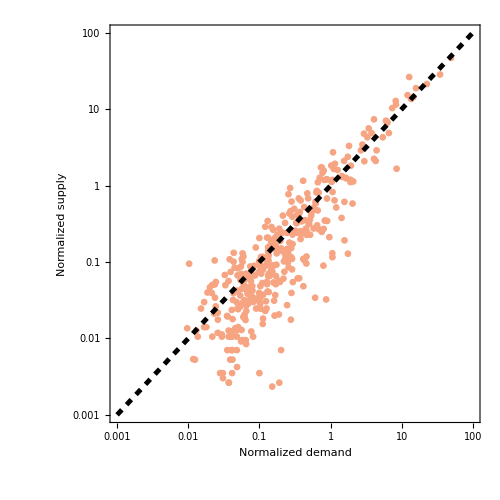

```mathematica
Show[ImmigrationPlot,DiagonalPlot]
```

## Intellectual Property

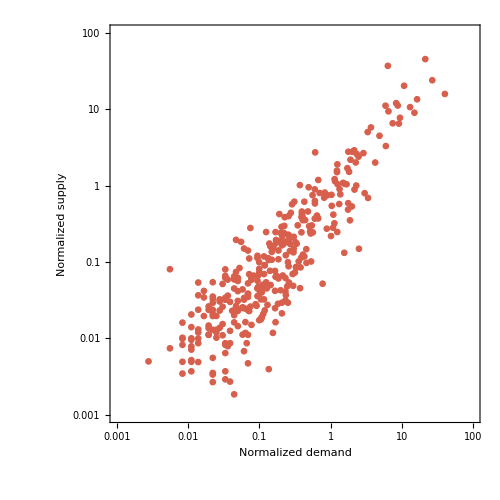

```mathematica
IntellectualPlot=ListLogLogPlot[IntellectualCollapse,PlotRange->{PlotRangeCollapse,PlotRangeCollapse},PlotMarkers->{Graphics[{FaceForm[colors[[5]]],EdgeForm[{colors[[5]],Opacity[opacity]}], Disk[]}],MarkerThickness},PlotTheme->"Scientific",FrameTicksStyle->Directive["Label",TextSize],FrameTicks->{{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"}},None},{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"}},None}},FrameLabel->{Style["Normalized demand",TextSize],Style["Normalized supply",TextSize]},PlotTheme-> "Scientific", 
FrameStyle->Directive[Thickness[.005]],LabelStyle->Directive[Black,FontFamily->{"Arial"}],AspectRatio->1,ImageSize->PlotSize]
```

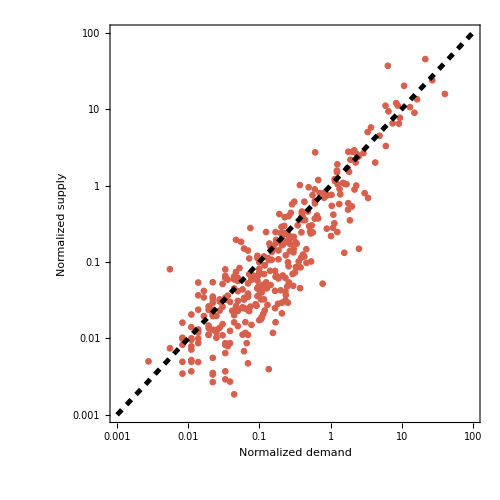

```mathematica
Show[IntellectualPlot,DiagonalPlot]
```

## Real Estate

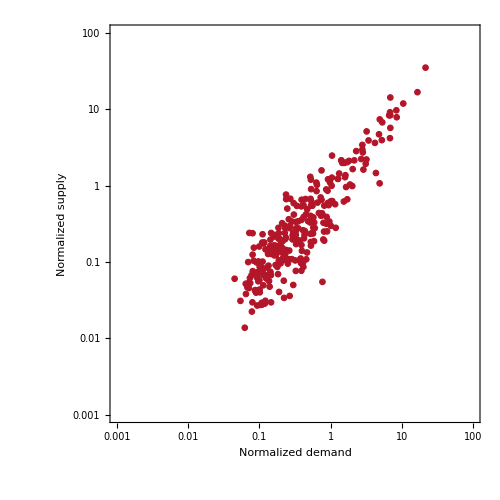

```mathematica
RealEstatePlot=ListLogLogPlot[RealEstateCollapse,PlotRange->{PlotRangeCollapse,PlotRangeCollapse},PlotMarkers->{Graphics[{FaceForm[colors[[6]]],EdgeForm[{colors[[6]],Opacity[opacity]}], Disk[]}],MarkerThickness},PlotTheme->"Scientific",FrameTicksStyle->Directive["Label",TextSize],FrameTicks->{{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"}},None},{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"}},None}},FrameLabel->{Style["Normalized demand",TextSize],Style["Normalized supply",TextSize]},PlotTheme-> "Scientific", 
FrameStyle->Directive[Thickness[.005]],LabelStyle->Directive[Black,FontFamily->{"Arial"}],AspectRatio->1,ImageSize->PlotSize]
```

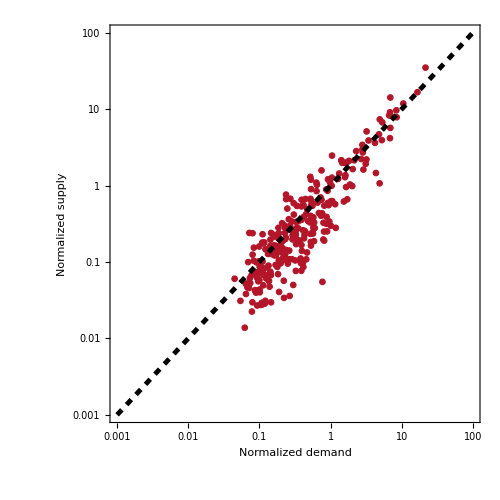

```mathematica
Show[RealEstatePlot,DiagonalPlot]
```

## Plot All

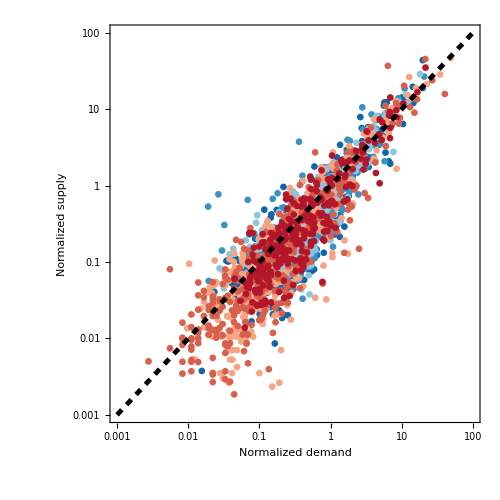

```mathematica
Show[BankruptcyPlot,CrimePlot,FamilyPlot,ImmigrationPlot,IntellectualPlot,RealEstatePlot,DiagonalPlot]
```

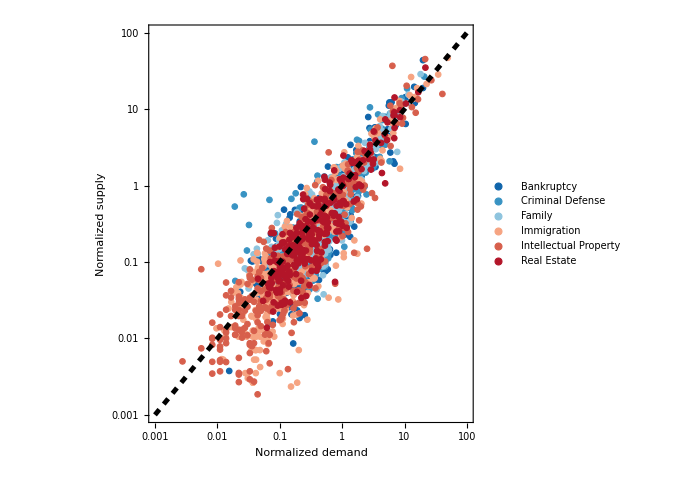

```mathematica
Legended[Show[BankruptcyPlot,CrimePlot,FamilyPlot,ImmigrationPlot,IntellectualPlot,RealEstatePlot,DiagonalPlot],Placed[PointLegend[{colors[[1]],colors[[2]],colors[[3]],colors[[4]],colors[[5]],colors[[6]]},{"Bankruptcy","Criminal Defense","Family","Immigration","Intellectual Property","Real Estate"},LegendMarkers->{{Graphics[{FaceForm[colors[[1]]],EdgeForm[{colors[[1]],Opacity[opacity]}], Disk[]}],6},{Graphics[{FaceForm[colors[[2]]],EdgeForm[{colors[[2]],Opacity[opacity]}], Disk[]}],6},{Graphics[{FaceForm[colors[[3]]],EdgeForm[{colors[[3]],Opacity[opacity]}], Disk[]}],6},{Graphics[{FaceForm[colors[[4]]],EdgeForm[{colors[[4]],Opacity[opacity]}], Disk[]}],6},{Graphics[{FaceForm[colors[[5]]],EdgeForm[{colors[[5]],Opacity[opacity]}], Disk[]}],6},{Graphics[{FaceForm[colors[[6]]],EdgeForm[{colors[[6]],Opacity[opacity]}], Disk[]}],6}},LabelStyle->Directive[FontFamily->{Bold,"Arial"},FontSize->TicksSize]],{0.23,0.8}]]
```